```mathematica
RUG[v_,phi_]:=RandomGraph[{v,Round[phi v (v-1)/2]}]
DAG[v_,phi_]:=DirectedGraph[RUG[v,phi],"Acyclic"]
EdgeToArray[e_]:={e[[1]],e[[2]]}
EList[G_]:=EdgeToArray/@(G//EdgeList)
Clean[from_][L_]:=Select[L,#[[1]]==from&]
IList[G_,v_]:=Last/@Clean[#][IncidenceList[G,#]]&/@Range[v]
```

```mathematica
ConnectComponents[{a_,b_}]:=DirectedEdge[RandomChoice[a],RandomChoice[b]];
ConnectedGraph[n_,m_,o___]:=Module[{vertices=n,edges=m,options=o},rg=RandomGraph[{vertices,edges},DirectedEdges->True];
cc=ConnectedComponents[rg];
edges=If[Length@cc≠1,ConnectComponents/@Partition[cc,2,1,1],{}];
Graph[DeleteDuplicates[edges~Join~EdgeList[rg]],Sequence@options]];
CUG[v_,phi_]:=ConnectedGraph[v,Round[phi v(v-1)/2]]

CUG[v_,phi_]:=Module[{g=RUG[v,phi]},While[Not[ConnectedGraphQ[g]],g=RUG[v,phi]];g];
```

```mathematica
ExportRUGS[]:=Export[ToString[#]<>"_MS",RUG[#,6/10]//AdjacencyMatrix,"Table",FieldSeparators->" "]&/@Range[100,2000,100]
ExportDAGS[]:=Export[ToString[#]<>"_DAG",G//IList[DAG[#,3/10],#] ,"Table",FieldSeparators->" "]&/@Range[100,1500,100]
ExportCUGSClass[phi_]:=Export[ToString[#]<>"_"<>ToString[Round[phi*100]],CUG[#,phi]//AdjacencyMatrix,"Table",FieldSeparators->" "]&/@Range[100,1500,100]
ExportCUGS[]:=ExportCUGSClass[#]&/@{0.1,0.2,0.3,0.4,0.6,0.8,0.95}
```

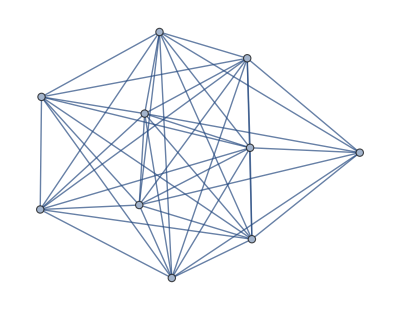

False

True

{{1<->5,5<->8,8<->2,2<->4,4<->7,7<->6,6<->9,9<->10,10<->3,3<->1}}

{}

```mathematica
G=CUG[10,0.95]
AcyclicGraphQ[G]
ConnectedGraphQ[G]
FindHamiltonianCycle[G]
FindEulerianCycle[G]
```

```mathematica
ExportCUGS[]
```

{{100_10,200_10,300_10,400_10,500_10,600_10,700_10,800_10,900_10,1000_10,1100_10,1200_10,1300_10,1400_10,1500_10},{100_20,200_20,300_20,400_20,500_20,600_20,700_20,800_20,900_20,1000_20,1100_20,1200_20,1300_20,1400_20,1500_20},{100_30,200_30,300_30,400_30,500_30,600_30,700_30,800_30,900_30,1000_30,1100_30,1200_30,1300_30,1400_30,1500_30},{100_40,200_40,300_40,400_40,500_40,600_40,700_40,800_40,900_40,1000_40,1100_40,1200_40,1300_40,1400_40,1500_40},{100_60,200_60,300_60,400_60,500_60,600_60,700_60,800_60,900_60,1000_60,1100_60,1200_60,1300_60,1400_60,1500_60},{100_80,200_80,300_80,400_80,500_80,600_80,700_80,800_80,900_80,1000_80,1100_80,1200_80,1300_80,1400_80,1500_80},{100_95,200_95,300_95,400_95,500_95,600_95,700_95,800_95,900_95,1000_95,1100_95,1200_95,1300_95,1400_95,1500_95}}

```mathematica
(*
V,E,MAXIMUM E,Edge List,Adj List,Adj Matrix,Inc Matrix (all functions involved case):20 114 190 0 0 0 0
40 468 780 0 0 0 0
60 1062 1770 0.015 0.016 0 0
80 1896 3160 0.047 0.015 0 0.031
100 2970 4950 0.094 0.047 0 0.052
120 4284 7140 0.172 0.078 0 0.094
140 5838 9730 0.328 0.11 0 0.188
160 7632 12720 0.547 0.195 0 0.312
180 9666 16110 0.875 0.265 0 0.506
200 11940 19900 1.344 0.375 0 0.781
220 14454 24090 1.954 0.515 0 1.141
240 17208 28680 2.785 0.657 0 1.625
260 20202 33670 3.837 0.839 0 2.256
280 23436 39060 5.157 1.068 0 3.047
300 26910 44850 6.794 1.314 0 4.008
320 30624 51040 8.831 1.609 0 5.187
340 34578 57630 11.22 1.944 0 6.584
360 38772 64620 14.098 2.368 0 8.275
380 43206 72010 17.488 2.731 0 10.25
400 47880 79800 21.517 3.224 0 12.621
420 52794 87990 26.144 3.768 0 15.256
440 57948 96580 31.543 4.373 0 18.358
460 63342 105570 37.694 4.962 0 21.908
480 68976 114960 44.593 5.709 0 25.937
500 74850 124750 52.828 6.465 0 30.485
520 80964 134940 62.009 7.281 0 35.995
540 87318 145530 72.613 8.251 0 41.464
560 93912 156520 83.627 9.193 0 47.744
580 100746 167910 96.343 10.219 0 54.963
600 107820 179700 110.395 11.437 0 62.818
*)
```